## Functions and initial setup

InitMatrix gives a  recombination table (transmission matrrix) for 36 possible mating combinations of 6 male and female genotypes. This model has TARE only, so only one locus with three possible alleles - wildtype (w1), TARE(T), and TARE-resistant non-functional allele (S). The elements within each row are {Father genotype, Mother Genotype, Proportion of offspring with genotype 1, ... ,Proportion of offspring with genotype 6}. The genotype numbers correspond to the following order - w1/w1, w1/S, w1/T, T/T, T/S, S/S. 
This matrix is incorporated later as ‘OgMatrix’ in the code.

```mathematica
InitMatrix={{1,1,1.,0.,0.,0.,0.,0.},{1,2,0.5,0.5,0.,0.,0.,0.},{1,3,0.5,0.,0.5,0.,0.,0.},{1,4,0.,0.,1.,0.,0.,0.},{1,5,0.,0.5,0.5,0.,0.,0.},{1,6,0.,1.,0.,0.,0.,0.},{2,1,0.5,0.5,0.,0.,0.,0.},{2,2,0.25,0.5,0.,0.,0.,0.25},{2,3,0.25,0.25,0.25,0.,0.25,0.},{2,4,0.,0.,0.5,0.,0.5,0.},{2,5,0.,0.25,0.25,0.,0.25,0.25},{2,6,0.,0.5,0.,0.,0.,0.5},{3,1,0.5,0.,0.5,0.,0.,0.},{3,2,0.25,0.25,0.25,0.,0.25,0.},{3,3,0.25,0.,0.5,0.25,0.,0.},{3,4,0.,0.,0.5,0.5,0.,0.},{3,5,0.,0.25,0.25,0.25,0.25,0.},{3,6,0.,0.5,0.,0.,0.5,0.},{4,1,0.,0.,1.,0.,0.,0.},{4,2,0.,0.,0.5,0.,0.5,0.},{4,3,0.,0.,0.5,0.5,0.,0.},{4,4,0.,0.,0.,1.,0.,0.},{4,5,0.,0.,0.,0.5,0.5,0.},{4,6,0.,0.,0.,0.,1.,0.},{5,1,0.,0.5,0.5,0.,0.,0.},{5,2,0.,0.25,0.25,0.,0.25,0.25},{5,3,0.,0.25,0.25,0.25,0.25,0.},{5,4,0.,0.,0.,0.5,0.5,0.},{5,5,0.,0.,0.,0.25,0.5,0.25},{5,6,0.,0.,0.,0.,0.5,0.5},{6,1,0.,1.,0.,0.,0.,0.},{6,2,0.,0.5,0.,0.,0.,0.5},{6,3,0.,0.5,0.,0.,0.5,0.},{6,4,0.,0.,0.,0.,1.,0.},{6,5,0.,0.,0.,0.,0.5,0.5},{6,6,0.,0.,0.,0.,0.,1.}};
```

### Phenotype numbers from four different cages

Each row gives {Number of TARE carriers, Number of wildtype phenotype} in each discrete generation. Data shown here is only until TARE was present in all individuals (TARE homozygotes + heterozygotes).

```mathematica
CageDataInd[1]={{1024,3029},{1346,3596},{1199,2591},{1205,2209},{1935,2387},{1303,817},{1750,663},{3668,1015},{1888,359},{3584,361},{4453,229},{3942,28},{3650,3},{3280,0}};

CageDataInd[2]={{1485,3494},{1236,2363},{2048,2981},{801,938},{2407,1596},{1830,621},{1722,642},{1916,552},{3375,747},{2941,495},{4173,494},{3179,208},{4860,159},{3333,19},{2879,0}};

CageDataInd[3]={{980,3302},{668,2053},{478,2059},{704,2765},{1013,3989},{442,1571},{1175,3643},{401,1156},{219,628},{1197,3431},{554,1478},{1225,3044},{911,2256},{596,1450}};

CageDataInd[4]={{402,2262},{219,2008},{513,4294},{490,4116},{500,4297},{287,2230},{624,4872},{312,2746},{357,2966},{248,2011},{360,2741}};
```

### Gene drive and selection functions

TareGerm, when called, executes germline TARE action (TARE disruption) on the GenoFreq list. GenoFreq is an array of 6 genotype frequencies that add up to 1. ‘x’ is the germline cut rate of wildtype alleles in genotypes that carry a copy of TARE.

```mathematica
TareGerm:=Function[{x} ,
(GenoFreq[[5]]=GenoFreq[[5]]+GenoFreq[[3]]*x;
GenoFreq[[3]]=GenoFreq[[3]]*(1-x);)];
```

TareEmbryo, when called, executes Embryonic TARE action (TARE disruption) on the GenoFreq list. ‘y’ is the embryonic cut rate of wildtype alleles in the embryos of mothers that carry TARE due to maternal deposition of the Cas9-gRNA complex. Note: Paternal deposition of Cas9 is assumed to be absent.

```mathematica
TareEmbryo:=Function[{y},(
GenoFreq[[5]]=GenoFreq[[5]]+GenoFreq[[3]]*y;
GenoFreq[[6]]=GenoFreq[[6]]+GenoFreq[[1]]*y^2+GenoFreq[[2]]*y;
GenoFreq[[2]]=GenoFreq[[2]]*(1-y)+2*GenoFreq[[1]]*y*(1-y);
GenoFreq[[1]]=GenoFreq[[1]]*(1-y)^2;
GenoFreq[[3]]=GenoFreq[[3]]*(1-y);
)];
```

The genMatrix function modifies the transmission matrix (OgMatrix) for mating genotype pairs based on the values of x, y. It puts in the effect of germline TARE and embryonic TARE. The final transmission matrix is called ‘NewMatrix’. This ‘NewMatrix’ will be used in the Step functions, where the GenMatrix function is called.

```mathematica
GenMatrix:=Function[{x,y},(

(*creating a temporary matrix from the original transmission matrix (i.e. recombination table). OgMatrix is the original recombination table (OgMatrix=InitMatrix assigned before this function is called)*)
NewMatrix=OgMatrix;
Do[
(* The code below creates a temporary new mating pair, calculates the progeny for them, and modifies the progeny genotype for the original mating pair in the transmission matrix *)

(* first germline TARE will modify NewMatrix if the parents have genotype Tw1 (genotype 3)*)
If[NewMatrix[[i,1]]==3||NewMatrix[[i,2]]==3,

If[(*TARE in both male and female*)
NewMatrix[[i,1]]==3 && NewMatrix[[i,2]]==3,
GenoFreq=Table[0,6];
GenoFreq[[NewMatrix[[i,1]]]]=1;
TareGerm[x];
NewMale=GenoFreq;

GenoFreq=Table[0,6];
GenoFreq[[NewMatrix[[i,2]]]]=1;
TareGerm[x];
NewFemale=GenoFreq;,

If[(*TARE in male only*)
NewMatrix[[i,1]]==3 ,
GenoFreq=Table[0,6];
GenoFreq[[NewMatrix[[i,1]]]]=1;
TareGerm[x];
NewMale=GenoFreq;
NewFemale=Table[0,6];
NewFemale[[NewMatrix[[i,2]]]]=1;,

(*TARE in female only*)
GenoFreq=Table[0,6];
GenoFreq[[NewMatrix[[i,2]]]]=1;
TareGerm[x];
NewFemale=GenoFreq;
NewMale=Table[0,6];
NewMale[[NewMatrix[[i,1]]]]=1;]];

NewPair=Flatten[KroneckerProduct[NewMale,NewFemale]];
NewProgeny=NewPair*OgMatrix[[1;;Length[OgMatrix],3;;8]];
NewMatrix[[i,3;;8]]=Total[NewProgeny]/Total[NewProgeny,2];];

(*Embryonic TARE action can convert w1 to S if mom had a T*)
If[MemberQ[Range[3,5],NewMatrix[[i,2]]],
GenoFreq=NewMatrix[[i,3;;8]];
TareEmbryo[y];
NewMatrix[[i,3;;8]]=GenoFreq;]
,{i,1,Length[NewMatrix]}];
)];
```

Generate 6 mate choice fitness parameters for 6 male genotypes (based on the mate choice parameter ‘m’). The S allele has no phenotypic marker, so it is assumed not to be selected against by female mate choice. All females are assumed to discriminate against males that carry a green phenotype.

```mathematica
(*codominant multiplicative effect*)
MatingParaCodominant:=Function[{m},(
MatingPara=Table[1,6];
MatingPara[[3]]=Sqrt[m];
MatingPara[[4]]=m;
MatingPara[[5]]=Sqrt[m];
)];
(*dominant effect*)
MatingParaDominant:=Function[{m},(
MatingPara=Table[1,6];
MatingPara[[3]]=m;
MatingPara[[4]]=m;
MatingPara[[5]]=m;
)];
```

Generate 36 fecundity parameters for 36 mating pairs. The 36 parameters are 6 replicates of a set of 6 parameters since paternal genotypes are assumed to not matter for fecundity. NOTE: S is assumed to affect only viability, not fecundity.

```mathematica
(*codominant multiplicative effect*)
FecundityParaCodominant:=Function[{fT},(
FecundityPara=Table[1,6];
FecundityPara[[3]]=Sqrt[fT];
FecundityPara[[4]]=fT;
FecundityPara[[5]]=Sqrt[fT];
FecundityPara=Flatten[Table[FecundityPara,6]];
)];

(*dominant effect*)
FecundityParaDominant:=Function[{fT},(
FecundityPara=Table[1,6];
FecundityPara[[3]]=fT;
FecundityPara[[4]]=fT;
FecundityPara[[5]]=fT;
FecundityPara=Flatten[Table[FecundityPara,6]];
)];
```

Generate 12 viability parameters for 12 genotypes (6 for each sex). 
T locus is haplosufficient. SS individuals are not viable. Note that while vS is included as a parameter, it is always set equal to 1 in this mode because the TARE locus is fully haplosufficient. It is included only for future use with loci that are haplo-insufficient.

```mathematica
(*codominant multiplicative effect*)
(* 
assume v.w1T=sqrt(v.TT),
assume v.w1S=vS, Note: vS is always =1 in this model,
assume v.SS=0,
assume males and females have same viability
*)
ViabilityParaCodominant:=Function[{vT,vS},(
ViabilityPara=Table[1,6];
ViabilityPara[[2]]=vS;
ViabilityPara[[3]]=Sqrt[vT];
ViabilityPara[[4]]=vT;
ViabilityPara[[5]]=Sqrt[vT]*vS;
ViabilityPara[[6]]=0;
ViabilityPara=Flatten[Table[ViabilityPara,2]];
)];

(*dominant effect*)
(*
assume v.Dw2=v.DD
assume v.w1T=v.TT
assume v.w1S=vS, Note: vS is always =1 in this model
assume male and female have same viability
assume v.rr=v.w2r=v.Dr=0
assume v.SS=0
*)
ViabilityParaDominant:=Function[{vT,vS},(
ViabilityPara=Table[1,6];
ViabilityPara[[2]]=vS;
ViabilityPara[[3]]=vT;
ViabilityPara[[4]]=vT;
ViabilityPara[[5]]=vT*vS;
ViabilityPara[[6]]=0;
ViabilityPara=Flatten[Table[ViabilityPara,2]];
)];
```

### Step Functions

StartGenoFreq is a vector of 12 genotypic frequencies in the starting generation. Elements 1-6 are males, elements 7-12 are females.
The StepHelp function uses values from ‘StartGenoFreq’ as parental genotype frequencies and produces ‘Gen1GenoFreq’- a vector of genotype frequencies in generation 1 after mating, fecundity and viability selection has occurred.

```mathematica
StepHelp:=Function[{},(

(*Re-normalizing genotypic frequencies, just in case any machine errors were introduced*)
Male=StartGenoFreq[[1;;6]]/Total[StartGenoFreq[[1;;6]]];
Female=StartGenoFreq[[7;;12]]/Total[StartGenoFreq[[7;;12]]];

(*male frequencies are weighted by mating success*)
Male=Male*MatingPara/Total[Male*MatingPara];

(*incorporating the male and female frequencies into the transmission matrix*)
Pairs=Flatten[KroneckerProduct[Male,Female]];
Matrix0=TransMatrix[[All,3;;8]];
Matrix1=Pairs*Matrix0;

(*fecundity selection takes place here*)
Matrix1=FecundityPara*Matrix1;

(*viability selection takes place here*)
(*assuming autosomal locus. This 'Join' creates a 6x12 transmission matrix that has male and female progeny separately listed, in case male and female fitness parameters are different (which they are not in this version). The seemingly odd dimensions are because viability selection acts on offspring genotypes.*)
Matrix1=Join[Matrix1,Matrix1,2];

(*Note that fecundity and mate choice depends on parental genotype pair, while viability selection depends on offspring genotypes,thus requiring the transformation and retransformation of the matrix below.*)
Matrix1=Transpose[ViabilityPara*Transpose[Matrix1]];

(*'Gen1GenoFreq' is a 12 element vector of genotypic frequencies in males (1;;6) and females (7;;12)*)
Gen1GenoFreq=Total[Matrix1]/Total[Matrix1,2];
)];
```

The Step function could allow one to change the dominance pattern of different selection patterns. Here I have removed the option to select a pattern, instead simply making all fitness costs multiplicative (codominant). The pattern can be altered by changing the selection functions inside Step.

```mathematica
Step:=Function[{m,fT,vT,vS,x,y},(
OgMatrix=InitMatrix;
GenMatrix[x,y];
(*Reminder- NewMatrix is produced by the GenMatrix function, and is the transmission matrix that includes the effects of germline and embryonic cleavage by TARE *)
TransMatrix=NewMatrix;

(*MatingParaCodominant produces vector 'MatingPara' using value of m,
FecundityParaCodominant produces vector 'FecundityPara' using value of fT,
ViabilityParaCodominant produces vector 'ViabilityPara' using value of vT and vS for codominant effect*)(*Note: vS is always set as 1 in this model*)
MatingParaCodominant[m];
FecundityParaCodominant[fT];
ViabilityParaCodominant[vT,vS];
StepHelp[]

(*This will produce the 12-element 'Gen1GenoFreq' vector which gives genotype frequencies in generation 1 in males and females after all forms of selection*)
)];
```

### Genotype <-> Phenotype functions

This function converts the twelve predicted genotype frequencies into two predicted phenotypic frequencies.

```mathematica
TwelveToTwo:=Function[{},(

GreenPheno=Gen1GenoFreq[[3]]+Gen1GenoFreq[[4]]+Gen1GenoFreq[[5]]+Gen1GenoFreq[[9]]+Gen1GenoFreq[[10]]+Gen1GenoFreq[[11]];
WtPheno=Gen1GenoFreq[[1]]+Gen1GenoFreq[[2]]+Gen1GenoFreq[[6]]+Gen1GenoFreq[[7]]+Gen1GenoFreq[[8]]+Gen1GenoFreq[[12]];
Gen1PredictedPhenoFreq={GreenPheno,WtPheno}/(GreenPheno+WtPheno);
)];
```

This function converts two observed genotypic frequencies to 12 (estimated) genotypic frequencies based on predicted genotype frequencies and predicted phenotypic frequencies. The estimated genotypic frequencies are used in the loglikelihood generating function as parental genotype frequencies in all generations except the starting generation (where we know the parental genotypic frequencies)

```mathematica
(*Make sure this is NOT called before the Step function in the LogLGen loop, so that it does not apply to the starting generation*)
TwoToTwelve:=Function[{},(
ProgenyObsvPhenoFreq=ProgenyObsvPhenoFreq/Total[ProgenyObsvPhenoFreq];

(*This function is called within a loop that runs only after the starting generation. This function estimates the genotypic frequencies in a generation based on the phenotypic frequencies, and then sets that estimated set of genotypic frequencies as the starting frequencies, which get used as parental frequencies in subsequent generations. That is why StartGenoFreq is reset here. Note that this function is only used for logLikelihood estimation. It should not be used for plotting model fit, as it would defeate the purpose of testing the model fit based only on starting frequencies *)
StartGenoFreq=Gen1GenoFreq;
Do[
If[MemberQ[{3,4,5,9,10,11},i],If[Gen1PredictedPhenoFreq[[1]]>0,StartGenoFreq[[i]]=StartGenoFreq[[i]]/Gen1PredictedPhenoFreq[[1]]*ProgenyObsvPhenoFreq[[1]]]];
If[MemberQ[{1,2,6,7,8,12},i],If[Gen1PredictedPhenoFreq[[2]]>0,StartGenoFreq[[i]]=StartGenoFreq[[i]]/Gen1PredictedPhenoFreq[[2]]*ProgenyObsvPhenoFreq[[2]]]];
,{i,1,12}];

)];
```

### LogLikelihood generating functions

Rho function produces ‘R’, the LogLikelihood for a single generation transition. This is Eq. 5 in Liu, Champer et al. 2019.

```mathematica
Rho:=Function[{},(
Gen1PredictedPhenoFreq=Gen1PredictedPhenoFreq/Total[Gen1PredictedPhenoFreq];
ProgenyObsvPhenoFreq=ProgenyObsvPhenoFreq/Total[ProgenyObsvPhenoFreq];
ProgenyObsvPhenoNum=ProgenyObsvPhenoFreq*PopN;

LogA=Log[PopN]-Log[1-(Gen1PredictedPhenoFreq[[1]]^PopN+Gen1PredictedPhenoFreq[[2]]^PopN)/2];
R=LogA+LogGamma[PopN+1]-LogGamma[ProgenyObsvPhenoNum[[1]]+1]-LogGamma[ProgenyObsvPhenoNum[[2]]+1];
(*The If commands below ensure that Log[0] isn't attempted*)
If[Gen1PredictedPhenoFreq[[1]]>0,R+=ProgenyObsvPhenoNum[[1]]*Log[Gen1PredictedPhenoFreq[[1]]]];
If[Gen1PredictedPhenoFreq[[2]]>0,R+=ProgenyObsvPhenoNum[[2]]*Log[Gen1PredictedPhenoFreq[[2]]]];
)];
```

The LogL function iterates through all the generation transitions and calculates R for transitions to produce a combined LogLikelihood for the entire experiment (either all cages combined or individually for each cage depending on how the function is called. )

```mathematica
LogL:=Function[{Ne,m,fT,vT,vS,x,y},(

StartGenoFreq=Table[0,12];
StartingPhenoFreq=CageData[[1,All]]/Total[CageData[[1,All]]];
StartGenoFreq[[4]]=StartingPhenoFreq[[1]]/2;
StartGenoFreq[[10]]=StartingPhenoFreq[[1]]/2;
StartGenoFreq[[1]]=StartingPhenoFreq[[2]]/2;
StartGenoFreq[[7]]=StartingPhenoFreq[[2]]/2;

(*Here the first generation transition is simulated, but not used for calculationg the Max. Likelihood *)
ParentObsvPhenoFreq=CageData[[1,All]]/Total[CageData[[1,All]]];
ProgenyObsvPhenoFreq=CageData[[2,All]]/Total[CageData[[2,All]]];

If[NeMode=="avg", PopN=Ne*(Total[CageData[[1]]]+Total[CageData[[2]]] )/2,If[NeMode=="abs",PopN=Ne,Print["Wrong Ne Mode"]]];
Step[m,fT,vT,vS,x,y];
(*Step produces 'Gen1GenoFreq'*)
TwelveToTwo[];
(*TwelveToTwo uses 'Gen1GenoFreq' and produces 'Gen1PredictedPhenoFreq'*)
TwoToTwelve[];
(*TwoToTwelve uses 'ProgenyObsvPhenoFreq' and 'Gen1GenoFreq', and produces 'StartGenoFreq', which will be used as parental frequencies in the next generation*)

Do[
ParentObsvPhenoFreq=CageData[[i-1,All]]/Total[CageData[[i-1,All]]];
ProgenyObsvPhenoFreq=CageData[[i,All]]/Total[CageData[[i,All]]];

If[NeMode=="avg", PopN=Ne*(Total[CageData[[i-1]]]+Total[CageData[[i]]] )/2,If[NeMode=="abs",PopN=Ne,Print["Wrong Ne Mode"]]];
Step[m,fT,vT,vS,x,y];
(*Step produces 'Gen1GenoFreq'*)
TwelveToTwo[];
(*TwelveToTwo uses 'Gen1GenoFreq' and produces 'Gen1PredictedPhenoFreq'*)
TwoToTwelve[];
(*TwoToTwelve uses 'ProgenyObsvPhenoFreq' and 'Gen1GenoFreq', and produces 'StartGenoFreq', which will be used as parental frequencies in the next generation*)
Rho[];
LogLValue+=R;

,{i,3,Length[CageData]}]


)];
```

LogLGen creates an optimizable function with a single output of the LogLikelihood. This function can be used with Mathematica’s numerical optimization function NMaximize.

```mathematica
LogLGen[Ne_?NumericQ,m_?NumericQ,fT_?NumericQ,vT_?NumericQ,vS_?NumericQ,x_?NumericQ,y_?NumericQ]:=(LogLValue=0;Do[CageData=CageDataInd[cage];LogL[Ne,m,fT,vT,vS,x,y],{cage,CageStart,CageEnd}];
LogLValue);
```

## Optimization for Maximum LogLikelihood

Below the LogLikelihood is optimized under different models (combinations of different forms of selection and other parameters). NeMode= “abs” sets effective population as a single parameter that does not change across generations. NeMode= “avg” allows the effective population to change across generations, where the parameter Ne describes the effective population as a fraction of the mean census populations of the two generations in a transition (see code inside the LogL function). The two modes give fairly close estimates for the effective population size - 
‘abs’ mode: OverHat[Ne]=~67 (1.93% of 3478.7, the mean census pop size across all generations in all cages); 
‘avg’ mode: OverHat[Ne]= ~2% of mean census population (77 = 2% of 3478.7, the mean census pop size across all generations in all cages)

Note: vS describes the reduced fitness of individuals that carry a single copy of the non-functional allele at the TARE locus. In this model this locus is fully haplosufficient (i.e. a single copy of a functional allele T or w1 is sufficient for viability), and therefore vS is always set equal to 1. It is only included for possible future analyses of a haploinsufficient locus. The parameter is therefore does not affect, and is not included in the summary of any results.

```mathematica
Length[CageDataInd[1]]+Length[CageDataInd[2]]+Length[CageDataInd[3]]+Length[CageDataInd[4]]-8
```

46

### All cages combined

```mathematica
CageStart=1;
CageEnd=4;
```

#### Full Model (Nothing fixed)

precision and accuracy goals, and method needs to be specified for better optimization with these settings

```mathematica
NeMode="abs";
CageCombEstimateWithNe=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,0≤m≤1,0≤fT≤1,0≤vT≤1,vS==1,0≤x≤ 1,0≤y≤1},{Ne,m,fT,vT,vS,x,y},PrecisionGoal->3,AccuracyGoal->3, Method->"NelderMead"]
```

{98.9993,{Ne→130.714,m→0.999999,fT→0.76418,vT→0.934108,vS→1.,x→0.223096,y→0.935979}}

```mathematica
NeMode="avg";
CageCombEstimateWithNe=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,0≤m≤1,0≤fT≤1,0≤vT≤1,vS==1,0≤x≤ 1,0≤y≤1},{Ne,m,fT,vT,vS,x,y},PrecisionGoal->3,AccuracyGoal->3, Method->"NelderMead"]
```

{102.5,{Ne→0.0391829,m→0.908001,fT→0.976663,vT→1.,vS→1.,x→0.,y→0.752246}}

#### No selection (Everything but Ne fixed)

```mathematica
NeMode="abs";
CageCombEstimateWithNe=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,m==1,fT==1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y},PrecisionGoal->3,AccuracyGoal->3, Method->"NelderMead"]
```

{95.0909,{Ne→95.4134,m→1.,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimateWithNe=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,m==1,fT==1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y},PrecisionGoal->3,AccuracyGoal->3, Method->"NelderMead"]
```

{96.5336,{Ne→0.0302837,m→1.,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

#### All selection: cut rates fixed at experimentally calculated values

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,0≤m≤1,0≤fT≤1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{99.1141,{Ne→112.677,m→0.716128,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

precision and accuracy goals, and method needs to be specified for better optimization with the following settings

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,0≤m≤1,0≤fT≤1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y},PrecisionGoal->3,AccuracyGoal->3, Method->"NelderMead"]
```

{100.426,{Ne→0.0368582,m→0.942937,fT→0.846261,vT→0.962447,vS→1.,x→0.888,y→0.632}}

#### Simplified sexual and fecundity selection (m=fT)

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,0≤m≤1,fT==m,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{99.2645,{Ne→114.786,m→0.85974,fT→0.85974,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,0≤m≤1,fT==m,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{100.448,{Ne→0.035829,m→0.866633,fT→0.866633,vT→0.999846,vS→1.,x→0.888,y→0.632}}

#### No viability selection (vT fixed)

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,0≤m≤1,0≤fT≤1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{99.5544,{Ne→116.356,m→1.,fT→0.742475,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,0≤m≤1,0≤fT≤1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{100.753,{Ne→0.0364615,m→1.,fT→0.754112,vT→1.,vS→1.,x→0.888,y→0.632}}

#### No fecundity selection (fT fixed)

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,0≤m≤1,fT==1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{99.1161,{Ne→114.024,m→0.718048,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,0≤m≤1,fT==1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{100.279,{Ne→0.0356891,m→0.741251,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

#### No sexual selection (m fixed)

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,m==1,0≤fT≤1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{99.5544,{Ne→116.327,m→1.,fT→0.742478,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,m==1,0≤fT≤1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{100.753,{Ne→0.0364317,m→1.,fT→0.753959,vT→1.,vS→1.,x→0.888,y→0.632}}

#### Only sexual selection

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,0≤m≤1,fT==1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{99.1161,{Ne→114.018,m→0.718063,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,0≤m≤1,fT==1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{100.284,{Ne→0.0357033,m→0.732222,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

#### Only fecundity selection

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,m==1,0≤fT≤1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{99.5544,{Ne→116.327,m→1.,fT→0.742478,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,m==1,0≤fT≤1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{100.753,{Ne→0.0364615,m→1.,fT→0.754112,vT→1.,vS→1.,x→0.888,y→0.632}}

#### Only viability selection

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,m==1,fT==1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{98.7845,{Ne→112.444,m→1.,fT→1.,vT→0.844865,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,m==1,fT==1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{99.9906,{Ne→0.0352704,m→1.,fT→1.,vT→0.852885,vS→1.,x→0.888,y→0.632}}

#### Simplified sexual and fecundity selec only (fT=m, vT fixed)

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,0≤m≤1,fT==m,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{99.2645,{Ne→114.786,m→0.85974,fT→0.85974,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,0≤m≤1,fT==m,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{100.449,{Ne→0.035965,m→0.866934,fT→0.866934,vT→1.,vS→1.,x→0.888,y→0.632}}

### Cage 1 separate

```mathematica
CageStart=1;
CageEnd=1;
```

#### Full Model (Nothing fixed)

precision and accuracy goals, and method needs to be specified for better optimization with these settings

```mathematica
NeMode="abs";
CageCombEstimateWithNe=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,0≤m≤1,0≤fT≤1,0≤vT≤1,vS==1,0≤x≤ 1,0≤y≤1},{Ne,m,fT,vT,vS,x,y},PrecisionGoal->3,AccuracyGoal->3, Method->"DifferentialEvolution"]
```

{29.8833,{Ne→127.146,m→1.,fT→1.,vT→1.,vS→1.,x→4.86122×10^-9,y→0.874309}}

```mathematica
NeMode="avg";
CageCombEstimateWithNe=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,0≤m≤1,0≤fT≤1,0≤vT≤1,vS==1,0≤x≤ 1,0≤y≤1},{Ne,m,fT,vT,vS,x,y},PrecisionGoal->3,AccuracyGoal->3, Method->"NelderMead"]
```

{29.8291,{Ne→0.0363115,m→1.,fT→1.,vT→0.974192,vS→1.,x→0.421192,y→0.783731}}

#### No selection (Everything but Ne fixed)

```mathematica
NeMode="abs";
CageCombEstimateWithNe=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,m==1,fT==1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y},PrecisionGoal->3,AccuracyGoal->3, Method->"NelderMead"]
```

{29.6146,{Ne→121.326,m→1.,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimateWithNe=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,m==1,fT==1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y},PrecisionGoal->3,AccuracyGoal->3, Method->"NelderMead"]
```

{29.7723,{Ne→0.0351117,m→1.,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

#### All selection: cut rates fixed at experimentally calculated values

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,0≤m≤1,0≤fT≤1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y},Method->"DifferentialEvolution"]
```

{29.6146,{Ne→121.326,m→1.,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

precision and accuracy goals, and method needs to be specified for better optimization with the following settings

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,0≤m≤1,0≤fT≤1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y},PrecisionGoal->3,AccuracyGoal->3, Method->"NelderMead"]
```

{29.7723,{Ne→0.0351117,m→1.,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

#### Simplified sexual and fecundity selection (m=fT)

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,0≤m≤1,fT==m,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{29.6146,{Ne→121.326,m→1.,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,0≤m≤1,fT==m,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{29.7723,{Ne→0.0351117,m→1.,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

#### No viability selection (vT fixed)

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,0≤m≤1,0≤fT≤1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{29.6146,{Ne→121.326,m→1.,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,0≤m≤1,0≤fT≤1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{29.7723,{Ne→0.0351117,m→1.,fT→0.999999,vT→1.,vS→1.,x→0.888,y→0.632}}

#### No fecundity selection (fT fixed)

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,0≤m≤1,fT==1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{29.6146,{Ne→121.326,m→1.,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,0≤m≤1,fT==1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{29.7723,{Ne→0.0351117,m→1.,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

#### No sexual selection (m fixed)

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,m==1,0≤fT≤1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{29.6146,{Ne→121.325,m→1.,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,m==1,0≤fT≤1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{29.7723,{Ne→0.0351117,m→1.,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

#### Only sexual selection

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,0≤m≤1,fT==1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{29.6146,{Ne→121.326,m→1.,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,0≤m≤1,fT==1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{29.7723,{Ne→0.0351114,m→1.,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

#### Only fecundity selection

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,m==1,0≤fT≤1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{29.6146,{Ne→121.336,m→1.,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,m==1,0≤fT≤1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{29.7723,{Ne→0.0351117,m→1.,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

#### Only viability selection

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,m==1,fT==1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{29.6146,{Ne→121.326,m→1.,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,m==1,fT==1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{29.7723,{Ne→0.0351118,m→1.,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

#### Simplified sexual and fecundity selec only (fT=m, vT fixed)

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,0≤m≤1,fT==m,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{29.6146,{Ne→121.326,m→1.,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,0≤m≤1,fT==m,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{29.7723,{Ne→0.0351117,m→1.,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

### Cage 2 separate

```mathematica
CageStart=2;
CageEnd=2;
```

#### Full Model (Nothing fixed)

precision and accuracy goals, and method needs to be specified for better optimization with these settings

```mathematica
NeMode="abs";
CageCombEstimateWithNe=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,0≤m≤1,0≤fT≤1,0≤vT≤1,vS==1,0≤x≤ 1,0≤y≤1},{Ne,m,fT,vT,vS,x,y},PrecisionGoal->3,AccuracyGoal->3, Method->"DifferentialEvolution"]
```

{26.5694,{Ne→76.5035,m→1.,fT→1.,vT→1.,vS→1.,x→3.00579×10^-7,y→0.561998}}

```mathematica
NeMode="avg";
CageCombEstimateWithNe=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,0≤m≤1,0≤fT≤1,0≤vT≤1,vS==1,0≤x≤ 1,0≤y≤1},{Ne,m,fT,vT,vS,x,y},PrecisionGoal->3,AccuracyGoal->3, Method->"NelderMead"]
```

{26.0697,{Ne→0.0253153,m→0.99497,fT→0.777845,vT→1.,vS→1.,x→0.833518,y→0.265562}}

#### No selection (Everything but Ne fixed)

```mathematica
NeMode="abs";
CageCombEstimateWithNe=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,m==1,fT==1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y},PrecisionGoal->3,AccuracyGoal->3, Method->"NelderMead"]
```

{23.2732,{Ne→42.2091,m→1.,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimateWithNe=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,m==1,fT==1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y},PrecisionGoal->3,AccuracyGoal->3, Method->"NelderMead"]
```

{23.7239,{Ne→0.0134727,m→1.,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

#### All selection: cut rates fixed at experimentally calculated values

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,0≤m≤1,0≤fT≤1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{25.208,{Ne→59.7634,m→1.,fT→0.622664,vT→1.,vS→1.,x→0.888,y→0.632}}

precision and accuracy goals, and method needs to be specified for better optimization with the folloowing settings

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,0≤m≤1,0≤fT≤1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y},PrecisionGoal->3,AccuracyGoal->3, Method->"NelderMead"]
```

{25.6561,{Ne→0.0190347,m→1.,fT→0.633271,vT→1.,vS→1.,x→0.888,y→0.632}}

#### Simplified sexual and fecundity selection (m=fT)

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,0≤m≤1,fT==m,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{25.0507,{Ne→58.1078,m→0.783732,fT→0.783732,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,0≤m≤1,fT==m,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{25.4918,{Ne→0.018495,m→0.790792,fT→0.790792,vT→1.,vS→1.,x→0.888,y→0.632}}

#### No viability selection (vT fixed)

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,0≤m≤1,0≤fT≤1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{25.208,{Ne→59.7634,m→1.,fT→0.622664,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,0≤m≤1,0≤fT≤1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{25.6561,{Ne→0.0190347,m→1.,fT→0.633271,vT→1.,vS→1.,x→0.888,y→0.632}}

#### No fecundity selection (fT fixed)

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,0≤m≤1,fT==1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{25.0037,{Ne→57.6695,m→0.572833,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,0≤m≤1,fT==1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{25.4395,{Ne→0.0183405,m→0.585605,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

#### No sexual selection (m fixed)

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,m==1,0≤fT≤1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{25.208,{Ne→59.7634,m→1.,fT→0.622664,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,m==1,0≤fT≤1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{25.6561,{Ne→0.0190347,m→1.,fT→0.633271,vT→1.,vS→1.,x→0.888,y→0.632}}

#### Only sexual selection

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,0≤m≤1,fT==1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{25.0037,{Ne→57.6695,m→0.572833,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,0≤m≤1,fT==1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{25.4395,{Ne→0.0183405,m→0.585606,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

#### Only fecundity selection

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,m==1,0≤fT≤1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{25.208,{Ne→59.7634,m→1.,fT→0.622664,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,m==1,0≤fT≤1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{25.6561,{Ne→0.0190347,m→1.,fT→0.633271,vT→1.,vS→1.,x→0.888,y→0.632}}

#### Only viability selection

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,m==1,fT==1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{24.8726,{Ne→56.4702,m→1.,fT→1.,vT→0.753199,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,m==1,fT==1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{25.3193,{Ne→0.0180001,m→1.,fT→1.,vT→0.760468,vS→1.,x→0.888,y→0.632}}

#### Simplified sexual and fecundity selec only (fT=m, vT fixed)

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,0≤m≤1,fT==m,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{25.0507,{Ne→58.1067,m→0.783733,fT→0.783733,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,0≤m≤1,fT==m,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{25.4918,{Ne→0.018495,m→0.790792,fT→0.790792,vT→1.,vS→1.,x→0.888,y→0.632}}

### Cage 3 separate

```mathematica
CageStart=3;
CageEnd=3;
```

#### Full Model (Nothing fixed)

precision and accuracy goals, and method needs to be specified for better optimization with these settings

```mathematica
NeMode="abs";
CageCombEstimateWithNe=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,0≤m≤1,0≤fT≤1,0≤vT≤1,vS==1,0≤x≤ 1,0≤y≤1},{Ne,m,fT,vT,vS,x,y},PrecisionGoal->3,AccuracyGoal->3, Method->"DifferentialEvolution"]
```

{30.0295,{Ne→470.612,m→0.713433,fT→1.,vT→1.,vS→1.,x→1.,y→2.15295×10^-8}}

```mathematica
NeMode="avg";
CageCombEstimateWithNe=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,0≤m≤1,0≤fT≤1,0≤vT≤1,vS==1,0≤x≤ 1,0≤y≤1},{Ne,m,fT,vT,vS,x,y},PrecisionGoal->3,AccuracyGoal->3, Method->"NelderMead"]
```

{29.1861,{Ne→0.171536,m→0.904597,fT→0.71452,vT→1.,vS→1.,x→1.,y→0.}}

#### No selection (Everything but Ne fixed)

```mathematica
NeMode="abs";
CageCombEstimateWithNe=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,m==1,fT==1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y},PrecisionGoal->3,AccuracyGoal->3, Method->"NelderMead"]
```

{23.5,{Ne→159.489,m→1.,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimateWithNe=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,m==1,fT==1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y},PrecisionGoal->3,AccuracyGoal->3, Method->"NelderMead"]
```

{23.9304,{Ne→0.0581536,m→1.,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

#### All selection: cut rates fixed at experimentally calculated values

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,0≤m≤1,0≤fT≤1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{29.3526,{Ne→421.667,m→1.,fT→0.638042,vT→1.,vS→1.,x→0.888,y→0.632}}

precision and accuracy goals, and method needs to be specified for better optimization with the following settings

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,0≤m≤1,0≤fT≤1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y},PrecisionGoal->3,AccuracyGoal->3, Method->"NelderMead"]
```

{29.5028,{Ne→0.146398,m→1.,fT→0.656807,vT→1.,vS→1.,x→0.888,y→0.632}}

#### Simplified sexual and fecundity selection (m=fT)

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,0≤m≤1,fT==m,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{29.244,{Ne→413.056,m→0.800838,fT→0.800838,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,0≤m≤1,fT==m,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{29.4028,{Ne→0.143988,m→0.811934,fT→0.811934,vT→1.,vS→1.,x→0.888,y→0.632}}

#### No viability selection (vT fixed)

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,0≤m≤1,0≤fT≤1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{29.3526,{Ne→420.576,m→1.,fT→0.638052,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,0≤m≤1,0≤fT≤1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{29.5028,{Ne→0.146398,m→1.,fT→0.656807,vT→1.,vS→1.,x→0.888,y→0.632}}

#### No fecundity selection (fT fixed)

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,0≤m≤1,fT==1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{29.2239,{Ne→411.682,m→0.615135,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,0≤m≤1,fT==1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{29.3813,{Ne→0.143475,m→0.634914,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

#### No sexual selection (m fixed)

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,m==1,0≤fT≤1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{29.3526,{Ne→420.576,m→1.,fT→0.638052,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,m==1,0≤fT≤1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{29.5028,{Ne→0.146398,m→1.,fT→0.656807,vT→1.,vS→1.,x→0.888,y→0.632}}

#### Only sexual selection

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,0≤m≤1,fT==1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{29.2239,{Ne→411.682,m→0.615135,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,0≤m≤1,fT==1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{29.3813,{Ne→0.143475,m→0.634914,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

#### Only fecundity selection

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,m==1,0≤fT≤1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{29.3526,{Ne→420.576,m→1.,fT→0.638052,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,m==1,0≤fT≤1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{29.5028,{Ne→0.146398,m→1.,fT→0.656807,vT→1.,vS→1.,x→0.888,y→0.632}}

#### Only viability selection

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,m==1,fT==1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{28.8863,{Ne→389.238,m→1.,fT→1.,vT→0.78087,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,m==1,fT==1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{29.0627,{Ne→0.136082,m→1.,fT→1.,vT→0.793328,vS→1.,x→0.888,y→0.632}}

#### Simplified sexual and fecundity selec only (fT=m, vT fixed)

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,0≤m≤1,fT==m,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{29.244,{Ne→413.056,m→0.800838,fT→0.800838,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,0≤m≤1,fT==m,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{29.4028,{Ne→0.143988,m→0.811934,fT→0.811934,vT→1.,vS→1.,x→0.888,y→0.632}}

### Cage 4 separate

```mathematica
CageStart=4;
CageEnd=4;
```

#### Full Model (Nothing fixed)

precision and accuracy goals, and method needs to be specified for better optimization with these settings

```mathematica
NeMode="abs";
CageCombEstimateWithNe=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,0≤m≤1,0≤fT≤1,0≤vT≤1,vS==1,0≤x≤ 1,0≤y≤1},{Ne,m,fT,vT,vS,x,y},PrecisionGoal->3,AccuracyGoal->3, Method->"DifferentialEvolution"]
```

{33.6547,{Ne→2934.62,m→1.,fT→1.,vT→1.,vS→1.,x→0.138121,y→0.24463}}

```mathematica
NeMode="avg";
CageCombEstimateWithNe=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,0≤m≤1,0≤fT≤1,0≤vT≤1,vS==1,0≤x≤ 1,0≤y≤1},{Ne,m,fT,vT,vS,x,y},PrecisionGoal->3,AccuracyGoal->3, Method->"DifferentialEvolution"]
```

{33.3455,{Ne→0.749712,m→1.,fT→1.,vT→1.,vS→1.,x→0.122705,y→0.135412}}

#### No selection (Everything but Ne fixed)

```mathematica
NeMode="abs";
CageCombEstimateWithNe=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,m==1,fT==1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y},PrecisionGoal->3,AccuracyGoal->3, Method->"NelderMead"]
```

{31.9047,{Ne→1990.22,m→1.,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimateWithNe=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,m==1,fT==1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y},PrecisionGoal->3,AccuracyGoal->3, Method->"NelderMead"]
```

{31.2566,{Ne→0.471618,m→1.,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

#### All selection: cut rates fixed at experimentally calculated values

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,0≤m≤1,0≤fT≤1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{33.3726,{Ne→2756.61,m→1.,fT→1.,vT→0.931219,vS→1.,x→0.888,y→0.632}}

precision and accuracy goals, and method needs to be specified for better optimization with the folloowing settings

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,0≤m≤1,0≤fT≤1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y},PrecisionGoal->3,AccuracyGoal->3, Method->"NelderMead"]
```

{32.9938,{Ne→0.693417,m→1.,fT→1.,vT→0.921739,vS→1.,x→0.888,y→0.632}}

#### Simplified sexual and fecundity selection (m=fT)

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,0≤m≤1,fT==m,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{33.3726,{Ne→2756.61,m→1.,fT→1.,vT→0.931219,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,0≤m≤1,fT==m,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{32.9938,{Ne→0.69342,m→1.,fT→1.,vT→0.921737,vS→1.,x→0.888,y→0.632}}

#### No viability selection (vT fixed)

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,0≤m≤1,0≤fT≤1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{33.3269,{Ne→2728.8,m→0.985021,fT→0.891043,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,0≤m≤1,0≤fT≤1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{32.9438,{Ne→0.685763,m→0.943995,fT→0.911472,vT→1.,vS→1.,x→0.888,y→0.632}}

#### No fecundity selection (fT fixed)

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,0≤m≤1,fT==1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{33.3726,{Ne→2756.61,m→0.999999,fT→1.,vT→0.931219,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,0≤m≤1,fT==1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{32.9938,{Ne→0.693456,m→1.,fT→1.,vT→0.921739,vS→1.,x→0.888,y→0.632}}

#### No sexual selection (m fixed)

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,m==1,0≤fT≤1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{33.3726,{Ne→2756.61,m→1.,fT→1.,vT→0.931219,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,m==1,0≤fT≤1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{32.9938,{Ne→0.693442,m→1.,fT→1.,vT→0.921737,vS→1.,x→0.888,y→0.632}}

#### Only sexual selection

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,0≤m≤1,fT==1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{33.3247,{Ne→2727.47,m→0.872621,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,0≤m≤1,fT==1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{32.9423,{Ne→0.685545,m→0.854746,fT→1.,vT→1.,vS→1.,x→0.888,y→0.632}}

#### Only fecundity selection

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,m==1,0≤fT≤1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{33.3268,{Ne→2728.78,m→1.,fT→0.877587,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,m==1,0≤fT≤1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{32.9433,{Ne→0.685683,m→1.,fT→0.860573,vT→1.,vS→1.,x→0.888,y→0.632}}

#### Only viability selection

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,m==1,fT==1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{33.3726,{Ne→2756.61,m→1.,fT→1.,vT→0.931219,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,m==1,fT==1,0≤vT≤1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{32.9938,{Ne→0.693417,m→1.,fT→1.,vT→0.921739,vS→1.,x→0.888,y→0.632}}

#### Simplified sexual and fecundity selec only (fT=m, vT fixed)

```mathematica
NeMode="abs";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne,0≤m≤1,fT==m,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{33.3265,{Ne→2728.55,m→0.936388,fT→0.936388,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
NeMode="avg";
CageCombEstimate=NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],0≤Ne≤1,0≤m≤1,fT==m,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{32.9437,{Ne→0.685756,m→0.927305,fT→0.927305,vT→1.,vS→1.,x→0.888,y→0.632}}

## Surface Plots and CI

#### LL surface for Ne & m=ft (best fit model)

{100.753,{Ne→0.0364615,m→1.,fT→0.754112,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
CageStart=1;
CageEnd=4;
NeMode="avg";
Ne=.;
m=1;
fT=.;
vT=1.;
vS=1.;
x=0.888;
y=0.632;
```

```mathematica
(*Plot3D[LogLGen[Ne,m,fT,vT,vS,x,y],{Ne,0.005,0.035},{fT,0.6,1}]*)
```

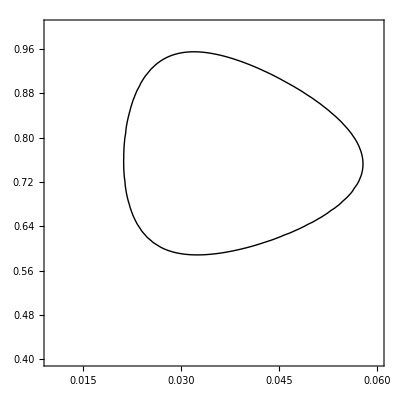

```mathematica
(*The 95% confidence interval is given values of m and Ne that produce LogLikelihood values within the Chi-square critical value for 2 degrees of freedom around the Max  LogLikelihood value. Contour is plotted at MaxLogLikelihood-2.9955*)
ConfInt=ContourPlot[LogLGen[Ne,m,fT,vT,vS,x,y],{Ne,0.01,0.06},{fT,0.4,1},Contours->{97.7575},ContourStyle->{Directive[Black,Thick]},ContourShading->None]
```

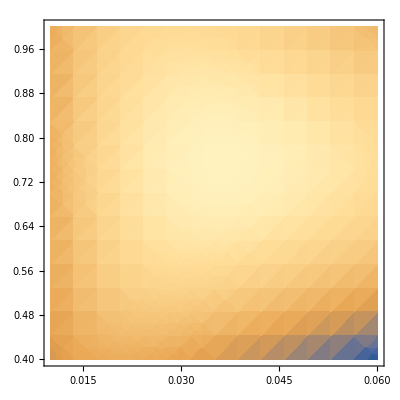

```mathematica
DensPlot=DensityPlot[LogLGen[Ne,m,fT,vT,vS,x,y],{Ne,0.01,0.06},{fT,0.4,1},PlotRange->All]
```

{100.753,{Ne→0.0364615,m→1.,fT→0.754112,vT→1.,vS→1.,x→0.888,y→0.632}}

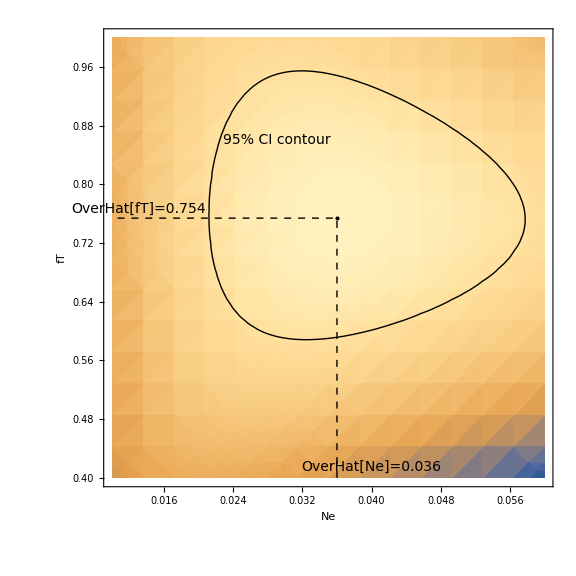

```mathematica
LLwithConfInt=Show[DensPlot,ConfInt,Epilog->{PointSize[Medium],Point[{0.036,0.754}],Dashed,Thick,Line[{{0.036,0.4},{0.036,0.754},{0.01,0.754}}],Text[Style["OverHat[Ne]=0.036",14],{0.04,0.415}],Text[Style["OverHat[fT]=0.754",14],{0.013,0.766}],Text[Style["95% CI contour",14,Black],{0.029,0.86}]},Frame->True,FrameLabel->{Style["Ne",14],Style["fT",14]},FrameStyle->Directive[Black,12,Thick,FontFamily->"Arial Baltic"],ImageSize->Large,ImagePadding->{{50,10},{50,10}}]
```

```mathematica
Export["fT Vs Ne LL with CI New.TIFF",LLwithConfInt,ImageResolution->300]
```

fT Vs Ne LL with CI New.TIFF

### Relationship between parameters m and fT (inability of MLE to distinguish between these)

The plot below shows the the inability of the MLE model to reliably distinguish between the parameters m and fT (note diagonal shape of the 95% confidence interval )

```mathematica
Clear[Ne,m,fT,vT,vS,x,y];
```

```mathematica
NMaximize[{LogLGen[Ne,m,fT,vT,vS,x,y],Ne==0.024,0≤m≤1,0≤fT≤1,vT==1,vS==1,x==0.888,y==0.632},{Ne,m,fT,vT,vS,x,y}]
```

{96.8263,{Ne→0.024,m→0.671548,fT→0.830833,vT→1.,vS→1.,x→0.888,y→0.632}}

Setting Ne at the MLE value and plotting ML across values of m and fT

```mathematica
NeMode="avg";
Ne=0.024;
m=.;
fT=.;
vT=1.;
vS=1.;
x=0.888;
y=0.632;
```

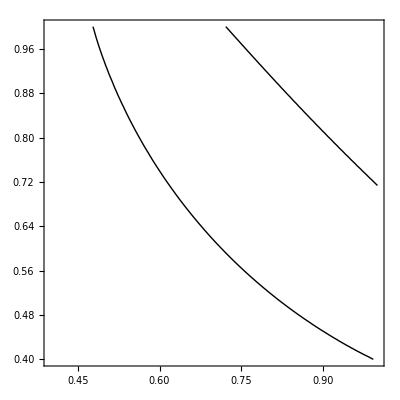

```mathematica
ConfIntMfT=ContourPlot[LogLGen[Ne,m,fT,vT,vS,x,y],{fT,0.4,1},{m,0.4,1},Contours->{93.8308},ContourStyle->{Directive[Black,Thick]},ContourShading->None]
```

```mathematica
Plot3D[LogLGen[Ne,m,fT,vT,vS,x,y],{fT,0.6,1},{m,0.6,1}]
```

-Graphics3D-

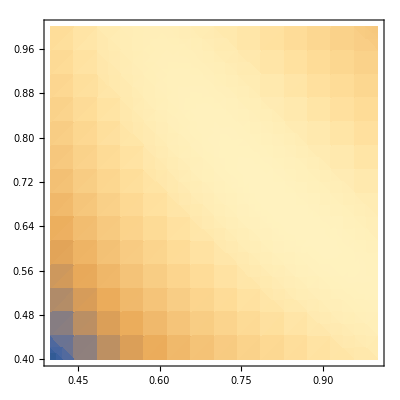

```mathematica
DensPlotMfT=DensityPlot[LogLGen[Ne,m,fT,vT,vS,x,y],{fT,0.4,1},{m,0.4,1},PlotRange->All]
```

{96.8263,{Ne→0.024,m→0.671548,fT→0.830833,vT→1.,vS→1.,x→0.888,y→0.632}}

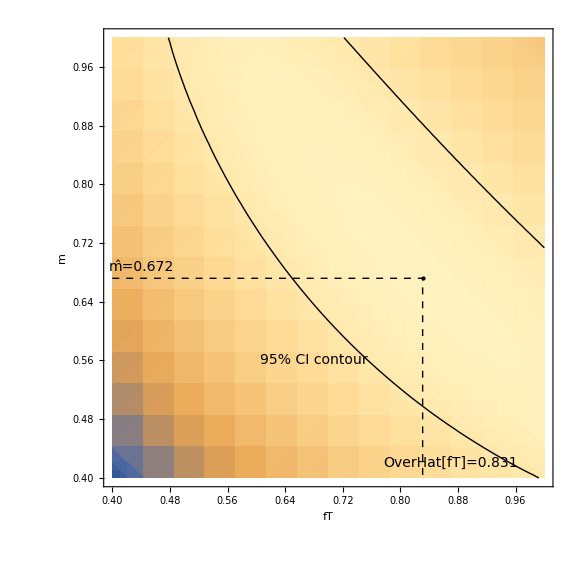

```mathematica
mfTPlot=Show[DensPlotMfT,ConfIntMfT,Epilog->{PointSize[Medium],Point[{0.831,0.672}],Dashed,Thick,Line[{{0.4,0.672},{0.831,0.672},{0.831,0.4}}],Text[Style["m̂=0.672",14],{0.44,0.688}],Text[Style["OverHat[fT]=0.831",14],{0.87,0.42}],Text[Style["95% CI contour",14,Black],{0.68,0.56}]},Frame->True,FrameLabel->{Style["fT",14,FontFamily->"Arial Baltic"],Style["m",14,FontFamily->"Arial Baltic"]},FrameStyle->Directive[Black,Thick,12],ImageSize->Large,ImagePadding->{{50,10},{50,10}}]
```

```mathematica
Export["fT vs m LL correlation.TIFF",mfTPlot,ImageResolution->300]
```

fT vs m LL correlation.TIFF

### Univariate 95% CI individually for Ne and m(=fT)

#### CI for Ne

{100.753,{Ne→0.0364615,m→1.,fT→0.754112,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
CageStart=1;
CageEnd=4;
NeMode="avg";
```

```mathematica
Clear[Ne,m,fT,vT,vS,x,y];
```

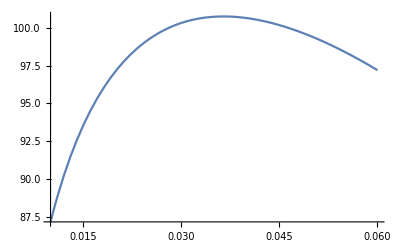

```mathematica
Plot[LogLGen[Ne,1,0.754112,1,1,0.888,0.632],{Ne,0.01,0.06}]
```

Lower 95% CI limit

```mathematica
FindRoot[LogLGen[Ne,1,0.754112,1,1,0.888,0.632]==98.8325,{Ne,0.01}]
```

{Ne→0.0237731}

Upper 95% CI limit

```mathematica
FindRoot[LogLGen[Ne,1,0.754112,1,1,0.888,0.632]==98.8325,{Ne,0.04}]
```

General::munfl: 0.016281^173.04 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.00207294^152.46 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.000208146^138.66 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{Ne→0.0530214}

```mathematica
1.9205
```

#### CI for fT

{100.753,{Ne→0.0364615,m→1.,fT→0.754112,vT→1.,vS→1.,x→0.888,y→0.632}}

```mathematica
Clear[Ne,m,fT,vT,vS,x,y];
```

```mathematica
CageStart=1;
CageEnd=4;
NeMode="avg";
```

```mathematica
Ne=0.0364615;
m=1.;
fT=.;
vT=1.;
vS=1.;
x=0.888;
y=0.632;
```

General::munfl: 0.0023453^138.973 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.000239344^126.394 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.00162327^113.596 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

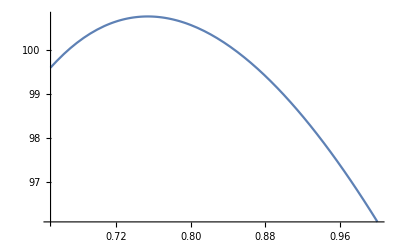

```mathematica
Plot[LogLGen[Ne,m,fT,vT,vS,x,y],{fT,0.65,1}]
```

```mathematica
100.75332538117873-1.9205
```

98.8328

Lower 95% CI limit

```mathematica
FindRoot[LogLGen[Ne,m,fT,vT,vS,x,y]==98.83282538117872,{fT,0.7}]
```

General::munfl: 0.0022064^138.973 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.000223383^126.394 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.00947646^152.61 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{fT→0.62237}

Upper 95% CI limit

```mathematica
FindRoot[LogLGen[Ne,m,fT,vT,vS,x,y]==98.83282538117872,{fT,0.9}]
```

General::munfl: 0.0017799^138.973 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.000175079^126.394 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0077165^152.61 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{fT→0.905907}